Experimenting with Raw Audio Data - Testing Functions

```mathematica
audioRawData = Import["/Users/shubhamkumar/Downloads/prenks/Summer Bummer Demo - LDR.mp3"]
```

```mathematica
Spectrogram[audioRawData]
```

-Graphics-

```mathematica
stereoTrimmedRawData = AudioChannelMix[trimmedAudioRawData, "Mono"]
```

1

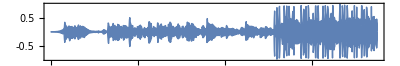

```mathematica
AudioChannels[stereoTrimmedRawData]
AudioPlot[stereoTrimmedRawData]
```

```mathematica
Audio[stereoTrimmedRawData, AudioChannelAssignment->{1}]
```

```mathematica
test = AudioGenerator["Sin", 10]
```

```mathematica
AudioChannels[test]
```

1

```mathematica
chanelledTest =Audio[test, AudioChannelAssignment->{2}]
```

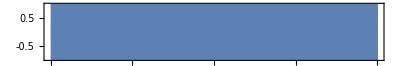

-Graphics-

```mathematica
AudioPlot[test]
AudioPlot[chanelledTest]
```

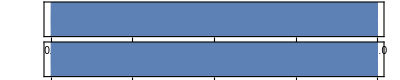

```mathematica
AudioPlot[AudioChannelMix[test, "Stereo"]]
```

```mathematica
a = Audio[AudioChannelMix[ExampleData[{"Audio", "FemaleVoice"}, "Audio"], "Mono"], AudioChannelAssignment -> {2}];
(*b=Audio[ExampleData[{"Audio","MaleVoice"},"Audio"], AudioChannelAssignment->{1}];*)
Export[ "/Users/shubhamkumar/Desktop/prenk.mp3",a]
```

/Users/shubhamkumar/Desktop/prenk.mp3

```mathematica
AudioChannelCombine[{a,b}]
```

```mathematica
AudioChannels/@{a,b}
```

{2,2}

Testing an 8D Audio File, visualizing Channels

```mathematica
spatialAudioSample = Import["/Users/shubhamkumar/Desktop/vb8d.mp3"]
```

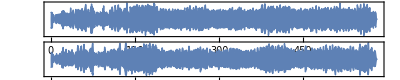

```mathematica
AudioPlot[spatialAudioSample]
```

```mathematica
Spectrogram[spatialAudioSample]
```

-Graphics-

```mathematica
Periodogram[AudioTrim[spatialAudioSample, {0,30}]]
```

-Graphics-

Testing Audio Panning

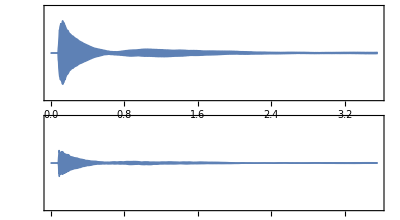

```mathematica
a=ExampleData[{"Sound","Piano"},"Audio"];
AudioPlot@a
```

```mathematica
a
```

```mathematica
spatialAudioSampleTrimmed = AudioTrim[spatialAudioSample, {0, 30}]
```

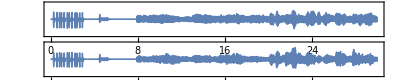

```mathematica
AudioPlot@spatialAudioSampleTrimmed
```

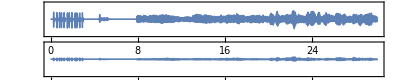

```mathematica
spatialAudioSampleTrimmedPanned =AudioPan[spatialAudioSampleTrimmed, -.75]
AudioPlot@spatialAudioSampleTrimmedPanned
```

Trying to Use Audio Pan with a Slider to Simulate Movement

```mathematica
spatialAudioSampleTrimmed
```

```mathematica
randomPans =RandomReal[{-1,1},30]
```

{0.242835,-0.133938,0.752118,0.135085,-0.225039,0.959682,-0.75473,0.839671,-0.33835,-0.170346,0.721687,-0.408207,-0.482115,-0.36058,0.121435,0.0841917,-0.841813,-0.183161,0.308849,0.439955,0.917713,0.749094,-0.434141,0.659666,-0.119764,0.515942,0.868239,0.50085,-0.45813,-0.292483}

```mathematica
splitAudio = AudioPartition[spatialAudioSampleTrimmed,1]
```

{,,,,,,,,,,,,,,,,,,,,,,,,,,,,,}

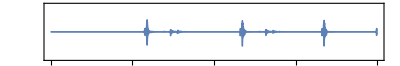
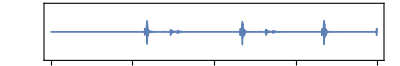
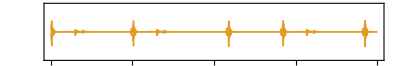
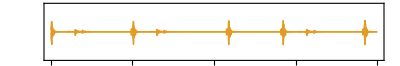
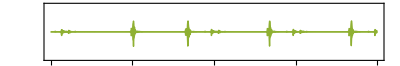
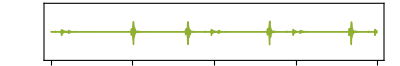
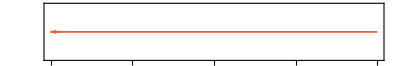
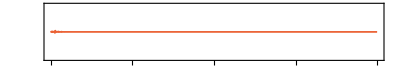
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-

```mathematica
AudioPlot@splitAudio
```

```mathematica
Panned = AudioJoin[MapThread[AudioPan[#1, #2]&,{splitAudio, Sin[#]/2.&/@ Table[Pi*x/2,{x,30}]}]]
```

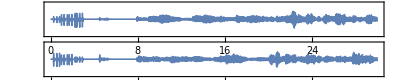

```mathematica
AudioPlot[Panned]
```

Testing how to map and generate lists with Sin because my brain is small

```mathematica
sum = MapThread[#1^2+#2^2&,{{1,2,3},{4,5,6}}]
```

{17,29,45}

```mathematica
testSinList =Sin[#]/2.&/@ Table[Pi*x/2,{x,30}]
```

{0.5,0.,-0.5,0.,0.5,0.,-0.5,0.,0.5,0.,-0.5,0.,0.5,0.,-0.5,0.,0.5,0.,-0.5,0.,0.5,0.,-0.5,0.,0.5,0.,-0.5,0.,0.5,0.}

```mathematica
Sin[Pi/3.]
```

0.866025